```mathematica
fDatasets = Association[];
fDatasetsNoEcho = Association[];
fDatasetsNaive = Association[];
```

```mathematica
sweepMax = 1200;
sweepStep = 30;
```

```mathematica
ϕxTarget = π/4;

κs = findκs[ϕxTarget];
κsNoEcho = findκsNoEcho[ϕxTarget];
κsNaive = findκsNaive[ϕxTarget];

fidelityData = Table[{δE, fidelity2D[RxGate[ϕxTarget, δE, κs], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
fidelityDataNoEcho = Table[{δE, fidelity2D[RxGateNoEcho[ϕxTarget, δE, κsNoEcho], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
fidelityDataNaive = Table[{δE, fidelity2D[RxGateNaive[ϕxTarget, δE, κsNaive], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
```

{6.24738,0.791962,6.28319,5.32923,0.999995}

{0.0306042,0.78564,6.28318,1.40943,1.}

{6.07738,0.785307,6.28318,5.37245,1.}

{{-1200,0.691784},{-1170,0.639139},{-1140,0.584324},{-1110,0.529375},{-1080,0.476609},{-1050,0.42854},{-1020,0.387778},{-990,0.356881},{-960,0.338188},{-930,0.333625},{-900,0.344498},{-870,0.37129},{-840,0.413482},{-810,0.469417},{-780,0.536237},{-750,0.60992},{-720,0.685432},{-690,0.757008},{-660,0.818576},{-630,0.86429},{-600,0.889143},{-570,0.889608},{-540,0.864228},{-510,0.814059},{-480,0.742887},{-450,0.657133},{-420,0.565393},{-390,0.477626},{-360,0.404025},{-330,0.353728},{-300,0.333535},{-270,0.346865},{-240,0.393162},{-210,0.467896},{-180,0.563177},{-150,0.668859},{-120,0.773887},{-90,0.867602},{-60,0.940784},{-30,0.986354},{0,0.999798},{30,0.979453},{60,0.926758},{90,0.846412},{120,0.746304},{150,0.636972},{180,0.530488},{210,0.438872},{240,0.37233},{270,0.337708},{300,0.33753},{330,0.369801},{360,0.42855},{390,0.50495},{420,0.588729},{450,0.66961},{480,0.738564},{510,0.788723},{540,0.815887},{570,0.818652},{600,0.798194},{630,0.757808},{660,0.702311},{690,0.637377},{720,0.56891},{750,0.502502},{780,0.443011},{810,0.394278},{840,0.358982},{870,0.338611},{900,0.333537},{930,0.343154},{960,0.36607},{990,0.400311},{1020,0.443528},{1050,0.493189},{1080,0.546748},{1110,0.601777},{1140,0.65607},{1170,0.707713},{1200,0.755126}}

```mathematica
{{-1200,0.608438139368806},{-1170,0.6805043370586097},{-1140,0.7525452973904004},{-1110,0.8200350881470717},{-1080,0.8789617365503953},{-1050,0.9267107041686637},{-1020,0.9619305218580007},{-990,0.9846756587160161},{-960,0.9960791855473407},{-930,0.9980399373763162},{-900,0.9928558685325959},{-870,0.9829082895936851},{-840,0.9704388322932402},{-810,0.9573573665323605},{-780,0.945177667665948},{-750,0.9349995139284624},{-720,0.927525086414788},{-690,0.9231012934610631},{-660,0.9217749400699602},{-630,0.9233514538687194},{-600,0.9274511665836466},{-570,0.9335652135067344},{-540,0.9411163143150114},{-510,0.9495052135107227},{-480,0.9581518802591846},{-450,0.966548375153514},{-420,0.9742857350217663},{-390,0.9810682773572703},{-360,0.9867257718114129},{-330,0.9912043344879777},{-300,0.9945532627471734},{-270,0.9968968935195357},{-240,0.9984132290781602},{-210,0.9992985312465721},{-180,0.9997486147297145},{-150,0.9999299434523476},{-120,0.9999761536400742},{-90,0.9999695146224294},{-60,0.9999452966431411},{-30,0.999894235966651},{0,0.9997739652226088},{30,0.9995233516133633},{60,0.9990783460923385},{90,0.9983888636709886},{120,0.9974343058796509},{150,0.996233514083949},{180,0.994857101935697},{210,0.9934028844462267},{240,0.9920049291740405},{270,0.9908127807806012},{300,0.9899548982886186},{330,0.9895200335298691},{360,0.9895334011939254},{390,0.9899187420626372},{420,0.9905115562020753},{450,0.9910195378129132},{480,0.9910493534651323},{510,0.9901219745435507},{540,0.9877021458480889},{570,0.9832347862821124},{600,0.976205085008673},{630,0.9662011495386498},{660,0.9529510348355276},{690,0.9363931177979216},{720,0.9167004822007885},{750,0.8943099174861162},{780,0.869911554384022},{810,0.844423213350681},{840,0.8189409619283451},{870,0.7946684443753719},{900,0.772841651462792},{930,0.7546407185882862},{960,0.7411342001068026},{990,0.733195715768782},{1020,0.7314959276759114},{1050,0.7363769529625683},{1080,0.7478391847497132},{1110,0.7655234067276189},{1140,0.78842995600332},{1170,0.8152167874859862},{1200,0.8436111841828982}};
AppendTo[fDatasets, π/4->%];
{{-1200,0.5784780664605167},{-1170,0.6285115068264739},{-1140,0.6777914035444754},{-1110,0.7245752339304588},{-1080,0.7671236972714388},{-1050,0.8038118557982107},{-1020,0.8332023759360887},{-990,0.8541063476668308},{-960,0.8656071297751701},{-930,0.8671070897022375},{-900,0.8583765891021031},{-870,0.8395835395418729},{-840,0.8112975162287249},{-810,0.7744833894397081},{-780,0.7304780196791392},{-750,0.6809516719976832},{-720,0.6278491354086851},{-690,0.5733192001726156},{-660,0.519628911978766},{-630,0.46907278885115256},{-600,0.42387449849251474},{-570,0.3860889874203748},{-540,0.3575095291115594},{-510,0.33958195724788365},{-480,0.3333342408136073},{-450,0.33932190017888614},{-420,0.35759300953361506},{-390,0.38767643055455603},{-360,0.42859149659923346},{-330,0.47888317038872624},{-300,0.5366761433247476},{-270,0.5997510504698591},{-240,0.6656373814666312},{-210,0.731715390907697},{-180,0.7953295047358823},{-150,0.8539029250768546},{-120,0.905049981166815},{-90,0.9466799882295338},{-60,0.977089383080422},{-30,0.9950359046764495},{0,0.9997941850755849},{30,0.9911867452120756},{60,0.9695902337416294},{90,0.9359186871259124},{120,0.8915795876291517},{150,0.8384115119174751},{180,0.7786054926517798},{210,0.71459063188337},{240,0.6489412128178009},{270,0.5842599300684076},{300,0.5230550534749768},{330,0.46763768709530706},{360,0.42002313712684514},{390,0.3818457461422772},{420,0.3542956019861006},{450,0.33807503549944085},{480,0.33337880411865906},{510,0.33989633743216285},{540,0.3568427999996829},{570,0.38300019500113025},{600,0.41678861669526884},{630,0.4563472848578888},{660,0.49961833847857207},{690,0.5444519780493349},{720,0.5886994893225244},{750,0.6303085306372704},{780,0.6674094706522871},{810,0.698390613782181},{840,0.7219585521065263},{870,0.7371832737184634},{900,0.7435241399624021},{930,0.7408395907336669},{960,0.7293757754877785},{990,0.709747539978788},{1020,0.6828999192998572},{1050,0.6500583229264845},{1080,0.6126607511306679},{1110,0.572298540322236},{1140,0.5306585672531603},{1170,0.48946484444471594},{1200,0.45038829540270975}};
AppendTo[fDatasetsNoEcho, π/4->%];
{{-1200,0.6917839857215071},{-1170,0.6391392631438251},{-1140,0.584324087767115},{-1110,0.5293754132793299},{-1080,0.47660853716983154},{-1050,0.42854007840276254},{-1020,0.38777792711696624},{-990,0.3568810446756294},{-960,0.33818837114539885},{-930,0.33362515968578604},{-900,0.3444978632219249},{-870,0.3712898946787708},{-840,0.4134817924962696},{-810,0.46941656624074846},{-780,0.5362369864524441},{-750,0.6099204125254886},{-720,0.685431633888249},{-690,0.7570075650519446},{-660,0.8185763950778226},{-630,0.8642902307614586},{-600,0.8891432919543247},{-570,0.8896083457750112},{-540,0.8642283290082032},{-510,0.8140590584074108},{-480,0.7428871802177541},{-450,0.6571326236760512},{-420,0.5653932381339519},{-390,0.477625592260453},{-360,0.40402456456041924},{-330,0.3537278154037805},{-300,0.333535012232801},{-270,0.3468650623983006},{-240,0.39316212863627864},{-210,0.46789602306897404},{-180,0.5631767435259242},{-150,0.6688589709938522},{-120,0.7738872575655101},{-90,0.8676023885450486},{-60,0.9407838658533771},{-30,0.9863537818138323},{0,0.9997979143154734},{30,0.9794532735592159},{60,0.9267577554071127},{90,0.8464118849324842},{120,0.7463044300884887},{150,0.6369724983480576},{180,0.5304881312801191},{210,0.43887208033246794},{240,0.3723301064570378},{270,0.33770807513630957},{300,0.3375304121190258},{330,0.3698007698303739},{360,0.4285500834638495},{390,0.5049503834102774},{420,0.5887288227716887},{450,0.669609771801902},{480,0.7385644603266576},{510,0.7887229459342278},{540,0.8158873172563563},{570,0.8186522809062465},{600,0.7981935944363677},{630,0.7578084231536085},{660,0.7023114665080371},{690,0.6373769175031453},{720,0.5689098586336311},{750,0.5025018542110655},{780,0.4430108332521713},{810,0.3942781606263339},{840,0.3589821586846032},{870,0.3386114003268219},{900,0.3335368383489732},{930,0.3431540477550281},{960,0.366070144560801},{990,0.4003109540836436},{1020,0.4435276898047145},{1050,0.49318909411161954},{1080,0.5467480889165498},{1110,0.6017767700429864},{1140,0.656069590126936},{1170,0.7077126673395459},{1200,0.7551261333019401}};
AppendTo[fDatasetsNaive, π/4->%];
```

```mathematica
ϕxTarget = π/2;

κs = findκs[ϕxTarget];
κsNoEcho = findκsNoEcho[ϕxTarget];
κsNaive = findκsNaive[ϕxTarget];

fidelityData = Table[{δE, fidelity2D[RxGate[ϕxTarget, δE, κs], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
fidelityDataNoEcho = Table[{δE, fidelity2D[RxGateNoEcho[ϕxTarget, δE, κsNoEcho], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
fidelityDataNaive = Table[{δE, fidelity2D[RxGateNaive[ϕxTarget, δE, κsNaive], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
```

{{-1200,1/6 (0.25 Tr[RxGate[π/2,-1200,findκs[π/2]].{{0,0},{0,2}}.ConjugateTranspose[RxGate[π/2,-1200,findκs[π/2]]].{{1,-ⅈ},{ⅈ,1}}]+0.25 Tr[RxGate[π/2,-1200,findκs[π/2]].{{1,-1},{-1,1}}.ConjugateTranspose[RxGate[π/2,-1200,findκs[π/2]]].{{1,-1},{-1,1}}]+0.25 Tr[1]+0.25 Tr[1]+0.25 Tr[RxGate[π/2,-1200,findκs[π/2]].{{1,1},{1,1}}.ConjugateTranspose[RxGate[π/2,-1200,findκs[π/2]]].{{1,1},{1,1}}]+0.25 Tr[RxGate[π/2,-1200,findκs[π/2]].{{2,0},{0,0}}.ConjugateTranspose[RxGate[π/2,-1200,findκs[π/2]]].{{1,ⅈ},{-ⅈ,1}}])},79,{1200,1/6 (1)}}
 |  |  |  |

{{-1200,1/6 (0.25 Tr[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]].{{0,0},{0,2}}.ConjugateTranspose[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]]].{{1,-ⅈ},{ⅈ,1}}]+0.25 Tr[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]].{{1,-1},{-1,1}}.ConjugateTranspose[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]]].{{1,-1},{-1,1}}]+1+1+0.25 Tr[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]].{1}.1.{{1,1},{1,1}}]+0.25 Tr[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]].{{2,0},{0,0}}.ConjugateTranspose[RxGateNoEcho[π/2,-1200,findκsNoEcho[π/2]]].{{1,ⅈ},{-ⅈ,1}}])},79,{1200,1}}
 |  |  |  |

{{-1200,1/6 (0.25 Tr[RxGateNaive[π/2,-1200,findκsNaive[π/2]].{{0,0},{0,2}}.ConjugateTranspose[RxGateNaive[π/2,-1200,findκsNaive[π/2]]].{{1,-ⅈ},{ⅈ,1}}]+0.25 Tr[RxGateNaive[π/2,-1200,findκsNaive[π/2]].{{1,-1},{-1,1}}.ConjugateTranspose[RxGateNaive[π/2,-1200,findκsNaive[π/2]]].{{1,-1},{-1,1}}]+0.25 1+1+0.25 Tr[RxGateNaive[π/2,-1200,findκsNaive[π/2]].{{1,1},{1,1}}.1.{{1,1},{1,1}}]+0.25 Tr[RxGateNaive[π/2,-1200,findκsNaive[π/2]].{{2,0},{0,0}}.ConjugateTranspose[RxGateNaive[π/2,-1200,findκsNaive[π/2]]].{{1,ⅈ},{-ⅈ,1}}])},79,{1200,1}}
 |  |  |  |

```mathematica
{{-sweepMax,0.9945851438272016},{-570,0.9958896857619883},{-540,0.9961805929688978},{-510,0.9958089549344411},{-480,0.9950891407049518},{-450,0.9942809445023524},{-420,0.9935783460712073},{-390,0.9931147134420143},{-360,0.9929596418154448},{-330,0.9931331276019068},{-300,0.9936055866398098},{-270,0.9943208304546594},{-240,0.9951981368086391},{-210,0.9961506381827991},{-180,0.9970887027456198},{-150,0.9979350939595012},{-120,0.9986398353923811},{-90,0.9991582642739891},{-60,0.9994794363629592},{-30,0.9996128996229507},{0,0.9995888273992646},{30,0.9994427751634679},{60,0.9992242706364826},{90,0.9989726150112483},{120,0.9987194744437621},{150,0.9984768114963579},{180,0.9982273247125237},{210,0.9979300886890733},{240,0.9975094307923178},{270,0.9968624650628929},{300,0.9958709822827856},{330,0.9944043762443702},{360,0.992336286889578},{390,0.9895510953538742},{420,0.9859708431364398},{450,0.9815603943433061},{480,0.9763333296882535},{510,0.970363240673247},{540,0.9637819733557706},{570,0.956777008627463},{sweepMax,0.9495864331884252}};
AppendTo[fDatasets, π/2->%];
{{-sweepMax,0.37623604517413545},{-570,0.3983662568652854},{-540,0.4249295005629192},{-510,0.4556470337467521},{-480,0.4901320523179652},{-450,0.5278936708943659},{-420,0.5683459407341904},{-390,0.6108204995512045},{-360,0.6545801167250143},{-330,0.6988372135576012},{-300,0.7427706095611395},{-270,0.7855459468917713},{-240,0.8263371578190976},{-210,0.8643445116260569},{-180,0.8988167336037569},{-150,0.9290679777878866},{-120,0.9544970372681771},{-90,0.9746011410402785},{-60,0.9889889668862663},{-30,0.9973912233470538},{0,0.999666691201156},{30,0.9958011298854221},{60,0.9859211897308119},{90,0.9702694823498099},{120,0.9492161915810349},{150,0.9232382550255358},{180,0.8929076931555353},{210,0.858876651475386},{240,0.8218581923139345},{270,0.782604490360993},{300,0.741890554329606},{330,0.7004877096102732},{360,0.6591457801479292},{390,0.6185733391557868},{420,0.579420566387233},{450,0.5422638283845975},{480,0.5075919359322065},{510,0.47580048748469306},{540,0.44718327750922005},{570,0.4219311618822438},{sweepMax,0.4001349140680597}};
AppendTo[fDatasetsNoEcho, π/2->%];
{{-sweepMax,0.5961365531261922},{-570,0.5638331487132869},{-540,0.5224086843644703},{-510,0.4755359533931736},{-480,0.42795771308769615},{-450,0.3850924314902928},{-420,0.3524805534694899},{-390,0.33511712364151536},{-360,0.3367636361511004},{-330,0.35935558076553825},{-300,0.4026322523590196},{-270,0.4640933978769779},{-240,0.5393224944134739},{-210,0.6226246785772447},{-180,0.7078405566719279},{-150,0.7891276037887917},{-120,0.8615271519208538},{-90,0.9212021551233778},{-60,0.9653651248997398},{-30,0.9920340077294935},{0,0.9997691928871079},{30,0.9875741477810053},{60,0.9550643905821914},{90,0.9028695843315577},{120,0.8331481361545694},{150,0.7499712183738035},{180,0.6593044727548714},{210,0.568508528529821},{240,0.48533880969401744},{270,0.4167057309461398},{300,0.3675436911354867},{330,0.3400692649746303},{360,0.33360756560183524},{390,0.3449594413765629},{420,0.36915621928139003},{450,0.4003893303109108},{480,0.4329102745147811},{510,0.46175953401692993},{540,0.48324740581115183},{570,0.4951758576083438},{sweepMax,0.49683255102733026}};
AppendTo[fDatasetsNaive, π/2->%];
```

```mathematica
ϕxTarget = 3π/4;

κs = findκs[ϕxTarget];
κsNoEcho = findκsNoEcho[ϕxTarget];
κsNaive = findκsNaive[ϕxTarget];

fidelityData = Table[{δE, fidelity2D[RxGate[ϕxTarget, δE, κs], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
fidelityDataNoEcho = Table[{δE, fidelity2D[RxGateNoEcho[ϕxTarget, δE, κsNoEcho], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
fidelityDataNaive = Table[{δE, fidelity2D[RxGateNaive[ϕxTarget, δE, κsNaive], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, sweepStep}]
```

{{-1200,1/6 (0.25 Tr[RxGate[(3 π)/4,-1200,findκs[(3 π)/4]].{{0,0},{0,2}}.ConjugateTranspose[RxGate[(3 π)/4,-1200,findκs[(3 π)/4]]].{{2 (-1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (ⅈ Cos[π/8]-Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8])),2 (-1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (-ⅈ Cos[π/8]+Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8]))},{2 (1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (ⅈ Cos[π/8]-Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8])),2 (1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (-ⅈ Cos[π/8]+Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8]))}}]+0.25 Tr[1]+0.25 Tr[1]+0.25 1+0.25 Tr[1]+0.25 Tr[1])},79,{1200,1/6 1}}
 |  |  |  |

{{-1200,1/6 (0.25 Tr[RxGateNoEcho[(3 π)/4,-1200,findκsNoEcho[(3 π)/4]].{{0,0},{0,2}}.ConjugateTranspose[RxGateNoEcho[(3 π)/4,-1200,findκsNoEcho[(3 π)/4]]].{{2 (-1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (ⅈ Cos[π/8]-Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8])),2 (-1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (-ⅈ Cos[π/8]+Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8]))},{2 (1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (ⅈ Cos[π/8]-Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8])),2 (1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (-ⅈ Cos[π/8]+Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8]))}}]+0.25 Tr[1]+0.25 1+1+0.25 Tr[1]+0.25 Tr[1])},79,{1200,1}}
 |  |  |  |

{{-1200,1/6 (0.25 Tr[RxGateNaive[(3 π)/4,-1200,findκsNaive[(3 π)/4]].{{0,0},{0,2}}.ConjugateTranspose[RxGateNaive[(3 π)/4,-1200,findκsNaive[(3 π)/4]]].{{2 (-1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (ⅈ Cos[π/8]-Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8])),2 (-1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (-ⅈ Cos[π/8]+Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8]))},{2 (1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (ⅈ Cos[π/8]-Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8])),2 (1/2 (-1)^(3/8)-1/2 (-1)^(5/8)) (1/2 (-ⅈ Cos[π/8]+Sin[π/8])+1/2 (ⅈ Cos[π/8]+Sin[π/8]))}}]+0.25 Tr[1]+0.25 1+1+0.25 Tr[1]+0.25 Tr[1])},79,{1200,1}}
 |  |  |  |

```mathematica
{{-sweepMax,0.9274029448226366},{-570,0.9329324064978284},{-540,0.9387892085781808},{-510,0.9448515414015671},{-480,0.9509907232527972},{-450,0.9570764693695673},{-420,0.9629866771000244},{-390,0.9686082033159407},{-360,0.9738478812810653},{-330,0.9786314256568605},{-300,0.9829059013578709},{-270,0.9866436564079335},{-240,0.9898360117008608},{-210,0.9924976378471555},{-180,0.9946541773369375},{-150,0.9963458859889698},{-120,0.9976314095723009},{-90,0.9985572632492021},{-60,0.9991812642195139},{-30,0.9995520176937341},{0,0.9997159404435526},{30,0.999703637225646},{60,0.9995337816926977},{90,0.999215118970801},{120,0.9987380241702463},{150,0.9980829877252095},{180,0.9972188566931752},{210,0.9961089464246167},{240,0.9947087032727162},{270,0.9929770379010506},{300,0.990877978172356},{330,0.9883858352388046},{360,0.9854897362060827},{390,0.9821865639946845},{420,0.9784995743276772},{450,0.9744704042249728},{480,0.9701529783712087},{510,0.9656174722046311},{540,0.9609470762284898},{570,0.9562301525016578},{sweepMax,0.9515594577972941}};
AppendTo[fDatasets, 3π/4->%];

{{-sweepMax,0.715222883743079},{-570,0.7377846126868948},{-540,0.7601414464449757},{-510,0.7821717402183213},{-480,0.8037512333753192},{-450,0.8247548444457232},{-420,0.845060958879854},{-390,0.864547467945462},{-360,0.8830997037196312},{-330,0.9006037613930058},{-300,0.9169556087232054},{-270,0.932054737315225},{-240,0.9458107887598306},{-210,0.9581416951006211},{-180,0.9689746599182414},{-150,0.9782470266334755},{-120,0.9859076073783497},{-90,0.9919168448878782},{-60,0.9962482167839709},{-30,0.9988850395642188},{0,0.9998269312317235},{30,0.9990842197379379},{60,0.9966829409907657},{90,0.9926615602846028},{120,0.9870706032245937},{150,0.9799743983516331},{180,0.9714504154180779},{210,0.9615846838386681},{240,0.950473847538136},{270,0.9382243384009441},{300,0.9249485970291642},{330,0.9107643400169572},{360,0.8957935703787753},{390,0.8801580480438798},{420,0.8639811062298228},{450,0.8473853893098999},{480,0.8304871514273295},{510,0.8134000824481007},{540,0.7962319710992001},{570,0.7790814705599921},{sweepMax,0.7620405056581153}};
AppendTo[fDatasetsNoEcho, 3π/4->%];

{{-sweepMax,0.3437875573103304},{-570,0.3365317342075137},{-540,0.33335264946200516},{-510,0.336237809833742},{-480,0.34706877393071833},{-450,0.3673798569493837},{-420,0.39810536022388715},{-390,0.4393544050324578},{-360,0.49026593821656506},{-330,0.5489924135664763},{-300,0.6128477380811955},{-270,0.6786146634350543},{-240,0.7429673711080286},{-210,0.802915562506328},{-180,0.8561621983279153},{-150,0.9012835076378881},{-120,0.9377027279764216},{-90,0.9654699296731042},{-60,0.984926498319123},{-30,0.9963634069948231},{0,0.9997612578454588},{30,0.9946644368390283},{60,0.980230733395205},{90,0.9554728341557587},{120,0.9196366934994917},{150,0.8726551561265975},{180,0.8155240010928457},{210,0.7505030624706897},{240,0.6809713575577536},{270,0.6109958455736242},{300,0.5447013650136219},{330,0.48561720785413975},{360,0.4361831606529652},{390,0.39752318604861436},{420,0.3694935626522591},{450,0.35094425106273675},{480,0.34008882709425614},{510,0.3348854800388287},{540,0.33335652952615946},{570,0.3338118474706576},{sweepMax,0.3349702612075641}};
AppendTo[fDatasetsNaive, 3π/4->%];
```

```mathematica
ϕxTarget = π;

κs = findκs[ϕxTarget];
κsNoEcho = findκsNoEcho[ϕxTarget];
κsNaive = findκsNaive[ϕxTarget];

fidelityData = Table[{δE, fidelity2D[RxGate[ϕxTarget, δE, κs], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, 30}]
fidelityDataNoEcho = Table[{δE, fidelity2D[RxGateNoEcho[ϕxTarget, δE, κsNoEcho], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, 30}]
fidelityDataNaive = Table[{δE, fidelity2D[RxGateNaive[ϕxTarget, δE, κsNaive], MatrixExp[-ⅈ*ϕxTarget*σX/2]]}, {δE, -sweepMax, sweepMax, 30}]
```

{6.24863,3.11143,6.28318,5.79898,0.999812}

{0.0988749,3.13152,6.28307,6.1508,0.999939}

{5.82858,3.13412,6.2831,5.73174,0.999994}

```mathematica
ϕPlot = π/4;
fidelityComparisonPlot[{fDatasetsNaive[ϕPlot], fDatasetsNoEcho[ϕPlot], fDatasets[ϕPlot]}, {"Naive", "Sweep", "Sweep & Echo"}, 1000]
(*ϕPlot = π/2;
fidelityComparisonPlot[{fDatasetsNaive[ϕPlot], fDatasetsNoEcho[ϕPlot], fDatasets[ϕPlot]}, {"Naive", "Sweep", "Sweep & Echo"}, 1000]
ϕPlot = 3π/4;
fidelityComparisonPlot[{fDatasetsNaive[ϕPlot], fDatasetsNoEcho[ϕPlot], fDatasets[ϕPlot]}, {"Naive", "Sweep", "Sweep & Echo"}, 1000]*)
```

-Graphics-

```mathematica
fidelityComparisonPlot[{fDatasets[π/4], fDatasets[π/2], fDatasets[3π/4]}, {"π/4", "π/2", "3π/4"}, 1000]
```

-Graphics-

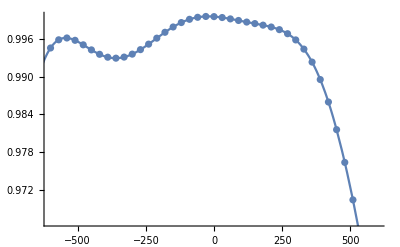

```mathematica
Interpolation[fDatasets[π/2], Method->"Spline"];
Show[ListPlot[fDatasets[π/2]], Plot[%[x], {x, -1000, 1000}]]
```

```mathematica
fDatasets[π/2]
Transpose[fDatasets[π/2]][[1]]
```

```mathematica
{{-sweepMax,0.9945851438272016},{-570,0.9958896857619883},{-540,0.9961805929688978},{-510,0.9958089549344411},{-480,0.9950891407049518},{-450,0.9942809445023524},{-420,0.9935783460712073},{-390,0.9931147134420143},{-360,0.9929596418154448},{-330,0.9931331276019068},{-300,0.9936055866398098},{-270,0.9943208304546594},{-240,0.9951981368086391},{-210,0.9961506381827991},{-180,0.9970887027456198},{-150,0.9979350939595012},{-120,0.9986398353923811},{-90,0.9991582642739891},{-60,0.9994794363629592},{-30,0.9996128996229507},{0,0.9995888273992646},{30,0.9994427751634679},{60,0.9992242706364826},{90,0.9989726150112483},{120,0.9987194744437621},{150,0.9984768114963579},{180,0.9982273247125237},{210,0.9979300886890733},{240,0.9975094307923178},{270,0.9968624650628929},{300,0.9958709822827856},{330,0.9944043762443702},{360,0.992336286889578},{390,0.9895510953538742},{420,0.9859708431364398},{450,0.9815603943433061},{480,0.9763333296882535},{510,0.970363240673247},{540,0.9637819733557706},{570,0.956777008627463},{sweepMax,0.9495864331884252}}
```

```mathematica
{-sweepMax,-570,-540,-510,-480,-450,-420,-390,-360,-330,-300,-270,-240,-210,-180,-150,-120,-90,-60,-30,0,30,60,90,120,150,180,210,240,270,300,330,360,390,420,450,480,510,540,570,sweepMax}
```